```mathematica
ClearAll[i,j,k]
```

```mathematica
spins={0,0,0,0,0}
```

{0,0,0,0,0}

```mathematica
energies=ConstantArray[0,{32}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Ns=ConstantArray[0,{32}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
spins[[1]]
```

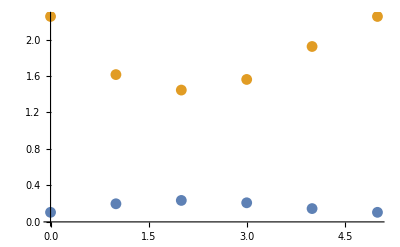

```mathematica
counter=0;
J=0.4;
epsilon=0.2;
Ns=ConstantArray[0,{32}];
energies=ConstantArray[0,{32}];
spins={0,0,0,0,0};
numerators={0,0,0,0,0,0};
PofN={{0,0},{1,0},{2,0},{3,0},{4,0},{5,0}};
FofN={{0,0},{1,0},{2,0},{3,0},{4,0},{5,0}};
Q=0;
For[i=-1,i≤1,i+=2,
	For[j=-1,j≤1,j+=2,
		For[k=-1,k≤1,k+=2,
			For[l=-1,l≤1,l+=2,
				For[m=-1,m≤1,m+=2,
				(*Print[i ,j, k, l, m];*)
					spins[[1]]=i;
					spins[[2]]=j; 
					spins[[3]]=k;
					spins[[4]]=l;
					spins[[5]]=m;
					ends = -J*spins[[1]]-J*spins[[5]];
					nnTerms=0;
					counter++;
					For[x=1,x≤4,x++,
						nnTerms += -J*spins[[x]]*spins[[x+1]];
					];
					tubeTerms=0;
					For[y=1,y≤5,y++,
						tubeTerms += (N[4*epsilon*J*spins[[y]]]-0);
						Ns[[counter]]+=(spins[[y]]+1)/2;
	
					];
					(*Print[N[tubeTerms]];*)
					etot=nnTerms+ends+tubeTerms;
					energies[[counter]]=etot
					(*Print[nnTerms,"   ",  tubeTerms ,"   ",  ends];*)
				];
		];
	];
];
];
For[z=1,z≤32,z++,
(*Print[z,"      ",       energies[[z]],"    ",Exp[-1*energies[[z]]],"   ",Q];*)
Q+=Exp[-1*energies[[z]]];
numerators[[Ns[[z]]+1]]+=Exp[-1*energies[[z]]];
(*Print[energies[[z]]];*)
];
For[q=1,q≤6,q++,
PofN[[q]][[2]]=numerators[[q]]/Q;
FofN[[q]][[2]]=-Log[PofN[[q]][[2]]];
];
ListPlot[{PofN,FofN}]
```

```mathematica
PofN
```

{{0,0.105044},{1,0.198756},{2,0.235521},{3,0.209605},{4,0.146031},{5,0.105044}}